```mathematica
(*Subscript[n, 1]=2.5;Subscript[n, 2]=1.5;
Subscript[ω, s][m_,θ_]:=1/(Subscript[n, 1] Sin[θ])(m π/2+ArcTan[(√(Subscript[n, 1]^2 Cos[θ]^2-Subscript[n, 2]^2))/(Subscript[n, 1] Sin[θ])]);
Subscript[ω, p][m_,θ_]:=1/(Subscript[n, 1] Sin[θ])(m π/2+ArcTan[(Subscript[n, 1] √(Subscript[n, 1]^2 Cos[θ]^2-Subscript[n, 2]^2))/(Subscript[n, 2]^2 Sin[θ])]);
Subscript[v, s][m_,θ_]:=Cos[θ]/Subscript[n, 1](1+1/(Subscript[ω, s][m,θ] √(Subscript[n, 1]^2 Cos[θ]^2-Subscript[n, 2]^2)))/(1+Cos[θ]^2/(Subscript[ω, s][m,θ] √(Subscript[n, 1]^2 Cos[θ]^2-Subscript[n, 2]^2)));
Subscript[v, p][m_,θ_]:=Cos[θ]/Subscript[n, 1](1+((Subscript[n, 1]^2-Subscript[n, 2]^2)Subscript[n, 2]^2)/(Subscript[ω, s][m,θ](Subscript[n, 1]^4 Cos[θ]^2+Subscript[n, 2]^4 Sin[θ]^2-Subscript[n, 1]^2 Subscript[n, 2]^2)√(Subscript[n, 1]^2 Cos[θ]^2-Subscript[n, 2]^2)))/(1+((Subscript[n, 1]^2-Subscript[n, 2]^2)Subscript[n, 2]^2 Cos[θ]^2)/(Subscript[ω, s][m,θ](Subscript[n, 1]^4 Cos[θ]^2+Subscript[n, 2]^4 Sin[θ]^2-Subscript[n, 1]^2 Subscript[n, 2]^2)√(Subscript[n, 1]^2 Cos[θ]^2-Subscript[n, 2]^2)));
Subscript[x, s][m_,θ_]:=2/(Subscript[ω, s][m,θ])Cot[θ]/(√(Subscript[n, 1]^2 Cos[θ]^2-Subscript[n, 2]^2));
Subscript[x, p][m_,θ_]:=2/(Subscript[ω, p][m,θ])((Subscript[n, 1]^2-Subscript[n, 2]^2)Subscript[n, 2]^2 Cot[θ])/((Subscript[n, 1]^4 Cos[θ]^2+Subscript[n, 2]^4 Sin[θ]^2-Subscript[n, 1]^2 Subscript[n, 2]^2)√(Subscript[n, 1]^2 Cos[θ]^2-Subscript[n, 2]^2));
Subscript[r, s][m_,θ_]:=(Subscript[n, 1]^2 Cos[θ]^2-Subscript[n, 2]^2)/(Subscript[n, 1]^2 Sin[θ]^2)(1+(-1)^m/Sinc[m π+2ArcTan[(√(Subscript[n, 1]^2 Cos[θ]^2-Subscript[n, 2]^2))/(Subscript[n, 1] Sin[θ])]]);
Subscript[η, s][m_,θ_]:=Subscript[r, s][m,θ]/(1+Subscript[r, s][m,θ]);
Subscript[r, p][m_,θ_]:=(Subscript[n, 1]^2 Cos[θ]^2-Subscript[n, 2]^2)/(Subscript[n, 1]^2 Sin[θ]^2)(1+(-1)^m/Sinc[m π+2ArcTan[(Subscript[n, 1] √(Subscript[n, 1]^2 Cos[θ]^2-Subscript[n, 2]^2))/(Subscript[n, 2]^2 Sin[θ])]]);
Subscript[η, p][m_,θ_]:=Subscript[r, s][m,θ]/(1+Subscript[r, s][m,θ]);
path="E://移动云盘同步盘//Desktop//笔记本//已转换笔记//波导//";
SolvePlot[{Subscript[ω, s][m,θ],Subscript[ω, p][m,θ],Subscript[v, s][m,θ],Subscript[v, p][m,θ],Subscript[x, s][m,θ],Subscript[x, p][m,θ],Subscript[η, s][m,θ],Subscript[η, p][m,θ]},{θ,0,ArcCos[Subscript[n, 2]/Subscript[n, 1]]},"params"->{"m","m",0},"change"->{{"m","absolute",0,1,2}},"axes"->{{"θ","ω_m^TEa / c"},{"θ","ω_m^TMa / c"},{"θ","v_m^TE / c"},{"θ","v_m^TM / c"},{"θ","D_m^TE / a"},{"θ","D_m^TM / a"},{"θ","η_m^TE"},{"θ","η_m^TM"}},"export"->{{path,"角频率TE关系"},{path,"角频率TM关系"},{path,"群速度TE关系"},{path,"群速度TM关系"},{path,"位移TE关系"},{path,"位移TM关系"},{path,"TE比率图"},{path,"TM比率图"}}]
*)
```

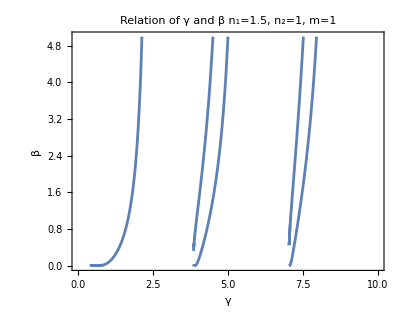

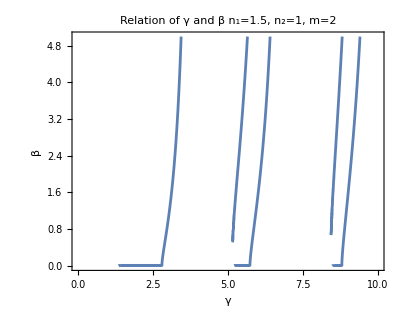

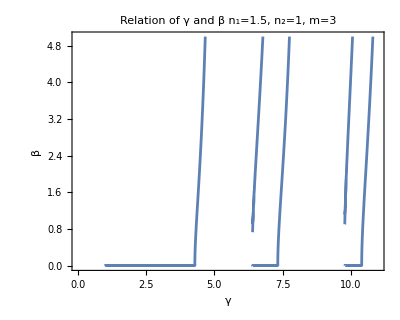

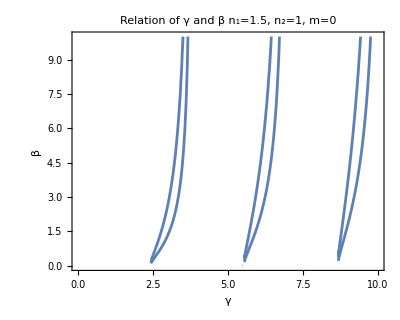

```mathematica
Clear["Global`*"];
f[ν_,expr_]:=Module[{x},(D[BesselJ[ν,x],x](BesselJ[ν,x]x)^-1)/. x->expr];
g[ν_,expr_]:=Module[{x},(D[BesselK[ν,x],x](BesselK[ν,x]x)^-1)/. x->expr];
Subscript[n, 1]=1.5;
Subscript[n, 2]=1;             
expr1[γ_,β_,m_]:=m^2(1/γ^2+1/β^2)(Subscript[n, 1]^2/γ^2+Subscript[n, 2]^2/β^2)-(Subscript[n, 1]^2 f[m,γ]+Subscript[n, 2]^2 g[m,β])(f[m,γ]+g[m,β]);
ContourPlot[expr1[γ,β,0]==0,{γ,0.00001,10},{β,0.00000001,10},PlotPoints->60,MaxRecursion->2,FrameLabel->{"γ","β"},PlotLabel->Column[{Style["Relation of γ and β ",14,FontFamily->"Times New Roman"],Style["n_1=1.5, n_2=1, m=0 \n",10,FontFamily->"Times New Roman"]},Alignment->Center],AspectRatio->0.8]
ContourPlot[expr1[γ,β,1]==0,{γ,0.00001,10},{β,0.00000001,5},PlotPoints->60,MaxRecursion->2,FrameLabel->{"γ","β"},PlotLabel->Column[{Style["Relation of γ and β ",14,FontFamily->"Times New Roman"],Style["n_1=1.5, n_2=1, m=1 \n",10,FontFamily->"Times New Roman"]},Alignment->Center],AspectRatio->0.8]
ContourPlot[expr1[γ,β,2]==0,{γ,0.00001,10},{β,0.00000001,5},PlotPoints->60,MaxRecursion->2,FrameLabel->{"γ","β"},PlotLabel->Column[{Style["Relation of γ and β ",14,FontFamily->"Times New Roman"],Style["n_1=1.5, n_2=1, m=2 \n",10,FontFamily->"Times New Roman"]},Alignment->Center],AspectRatio->0.8]
ContourPlot[expr1[γ,β,3]==0,{γ,0.00001,11},{β,0.00000001,5},PlotPoints->60,MaxRecursion->2,FrameLabel->{"γ","β"},PlotLabel->Column[{Style["Relation of γ and β ",14,FontFamily->"Times New Roman"],Style["n_1=1.5, n_2=1, m=3 \n",10,FontFamily->"Times New Roman"]},Alignment->Center],AspectRatio->0.8]
```

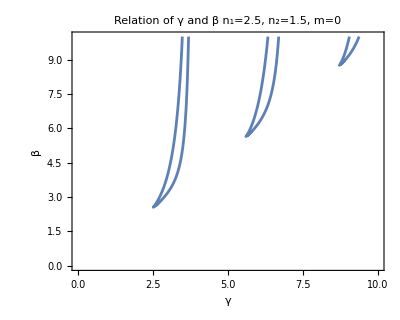

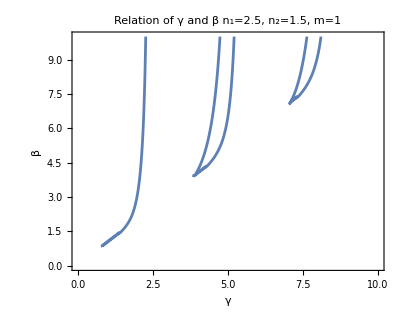

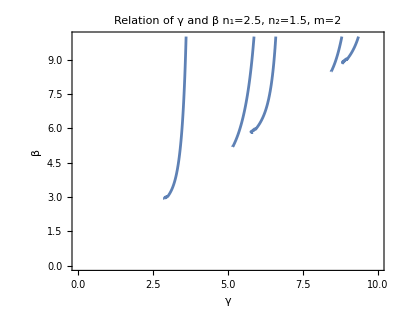

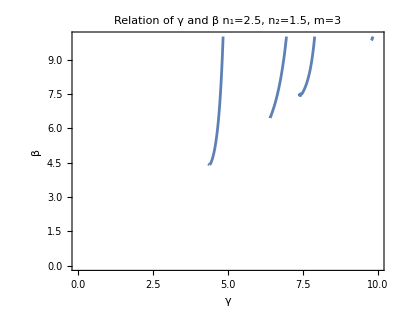

```mathematica
Clear["Global`*"];
f[ν_,expr_]:=Module[{x},(D[BesselJ[ν,x],x](BesselJ[ν,x]x)^-1)/. x->expr];
g[ν_,expr_]:=Module[{x},(D[BesselK[ν,x],x](BesselK[ν,x]x)^-1)/. x->expr];
Subscript[n, 1]=2.5;
Subscript[n, 2]=1.5;             
expr1[U_,V_,m_]:=m^2(1/U^2+1/(V^2-U^2))(Subscript[n, 1]^2/U^2+Subscript[n, 2]^2/(V^2-U^2))-(Subscript[n, 1]^2 f[m,U]+Subscript[n, 2]^2 g[m,√(V^2-U^2)])(f[m,U]+g[m,√(V^2-U^2)]);
ContourPlot[expr1[γ,β,0]==0,{β,0.00000001,10},{γ,0.00001,10},PlotPoints->60,MaxRecursion->2,FrameLabel->{"γ","β"},PlotLabel->Column[{Style["Relation of γ and β ",14,FontFamily->"Times New Roman"],Style["n_1=2.5, n_2=1.5, m=0 \n",10,FontFamily->"Times New Roman"]},Alignment->Center],AspectRatio->0.8]
ContourPlot[expr1[U,V,1]==0,{U,0.00000001,10},{V,0.00001,10},PlotPoints->60,MaxRecursion->2,FrameLabel->{"γ","β"},PlotLabel->Column[{Style["Relation of γ and β ",14,FontFamily->"Times New Roman"],Style["n_1=2.5, n_2=1.5, m=1 \n",10,FontFamily->"Times New Roman"]},Alignment->Center],AspectRatio->0.8]
ContourPlot[expr1[U,V,2]==0,{U,0.00000001,10},{V,0.00001,10},PlotPoints->60,MaxRecursion->2,FrameLabel->{"γ","β"},PlotLabel->Column[{Style["Relation of γ and β ",14,FontFamily->"Times New Roman"],Style["n_1=2.5, n_2=1.5, m=2 \n",10,FontFamily->"Times New Roman"]},Alignment->Center],AspectRatio->0.8]
ContourPlot[expr1[U,V,3]==0,{U,0.00000001,10},{V,0.00001,10},PlotPoints->60,MaxRecursion->2,FrameLabel->{"γ","β"},PlotLabel->Column[{Style["Relation of γ and β ",14,FontFamily->"Times New Roman"],Style["n_1=2.5, n_2=1.5, m=3 \n",10,FontFamily->"Times New Roman"]},Alignment->Center],AspectRatio->0.8]
```

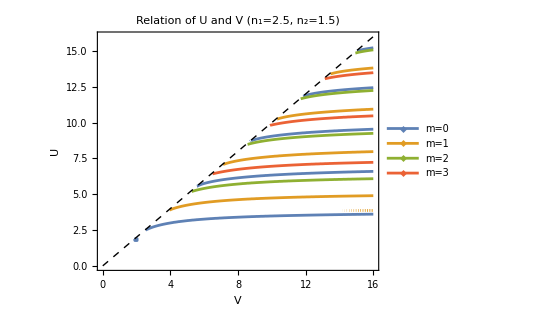

```mathematica
Clear["Global`*"];
f[ν_,expr_]:=Module[{x},(D[BesselJ[ν,x],x] (BesselJ[ν,x] x)^-1)/. x->expr];
g[ν_,expr_]:=Module[{x},(D[BesselK[ν,x],x] (BesselK[ν,x] x)^-1)/. x->expr];

Subscript[n,1]=2.5;
Subscript[n,2]=1.5;

expr1[U_,V_,m_]:=m^2 (1/U^2+1/(V^2-U^2)) (Subscript[n,1]^2/U^2+Subscript[n,2]^2/(V^2-U^2))-(Subscript[n,1]^2 f[m,U]+Subscript[n,2]^2 g[m,Sqrt[V^2-U^2]]) (f[m,U]+g[m,Sqrt[V^2-U^2]]);
expr2[U_,V_,m_]:=2Subscript[n,1]^2 f[m,U]+(Subscript[n,1]^2+Subscript[n,2]^2)g[m,Sqrt[V^2-U^2]]-√((Subscript[n,1]^2-Subscript[n,2]^2)^2 g[m,Sqrt[V^2-U^2]]^2+4Subscript[n,1]^2 m^2 (1/U^2+1/(V^2-U^2)) (Subscript[n,1]^2/U^2+Subscript[n,2]^2/(V^2-U^2)));
(*渐近线*)
asymptote=Graphics[{Dashed,Black,Line[{{0.001,0.001},{16,16}}]}];

(*主图*)
contour=ContourPlot[Evaluate@Table[expr2[U,V,m]==0,{m,0,3}],{V,0.0011,16},{U,0.001,16},PlotPoints->60,MaxRecursion->2,FrameLabel->{"V","U"},PlotLegends->Placed[LineLegend[{"m=0","m=1","m=2","m=3"},LegendMarkers->"◆"],Right],PlotLabel->Style["Relation of U and V (n₁=2.5, n₂=1.5)\n",14,FontFamily->"Times New Roman"],AspectRatio->0.8];

(*合并图层*)
Show[contour,asymptote]
```

```mathematica
(*创建表头：m阶/第几个零点*)header=Prepend[Table[ToString[n]<>"th zero ",{n,1,4}],"J_m(x)"];

zeros=Table[Prepend[Table[NumberForm[N[BesselJZero[m,n]],{10,4}],{n,1,4}],"m="<>ToString[m]],{m,0,3}];

(*合并表格*)
data=Prepend[zeros,header];

(*美观输出*)
Grid[data,Frame->All,Background->{None,{LightGray,{White,{GrayLevel[0.95]}}}},Spacings->{2,1},Alignment->Center,ItemStyle->{FontFamily->"Times New Roman",FontSize->14}]
```

J_m(x) | 1th zero  | 2th zero  | 3th zero  | 4th zero 
m=0 | 2.4048 | 5.5201 | 8.6537 | 11.7915
m=1 | 3.8317 | 7.0156 | 10.1735 | 13.3237
m=2 | 5.1356 | 8.4172 | 11.6198 | 14.7960
m=3 | 6.3802 | 9.7610 | 13.0152 | 16.2235